# Output: MCSLinv

```mathematica
countDat = Import[NotebookDirectory[],"MCSLoutputExample.csv"]; (* Edit here! *)
```

```mathematica
{a,b,c,ηaMean,μtMean} = Part[countDat,-5;;-1];
```

These two functions convert between ηa, μt space and μs, μa space.

```mathematica
μtηaToAS[point_]:=Module[{μt,ηa},{μt,ηa}=point;
 {(1-ηa)*μt,ηa μt}]
```

```mathematica
μtηaToASinv[point_]:=Module[{μs,μa},{μs,μa}=point;
 {μs+μa,μa/(μs+μa)}]
```

```mathematica
style[str_]:= Style[str,Black,Bold,14,FontFamily->"Helvetica"]
```

```mathematica
{μsMean,μaMean} = μtηaToAS[{μtMean,ηaMean}]//Flatten;
```

```mathematica
pointText = StringForm["(``, ``)",NumberForm[μsMean,3],NumberForm[μaMean,3]];
```

```mathematica
logLik[point_]:= Module[{μt,ηa},{μt,ηa}=point;
a(ηa-ηaMean)^2/2+b(ηa-ηaMean)(μt-μtMean)+c(μt-μtMean)^2/2]
```

Set the confidence interval:

```mathematica
p = .95; (* Edit here! *)
```

```mathematica
χ2= 0.5x/.FindRoot[CDF[ChiSquareDistribution[2],x]==p,{x,1}];
```

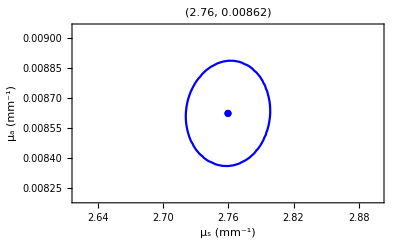

```mathematica
ellipse = Show[ContourPlot[-logLik[μtηaToASinv[{μs,μa}]]==χ2,{μs,μsMean*0.95,μsMean*1.05},{μa,μaMean*0.95,μaMean*1.05},ContourStyle-> Blue,PlotLabel-> style[pointText]],ListPlot[{{μsMean,μaMean}},PlotStyle-> Blue],AspectRatio->0.6,Frame-> True,FrameStyle->Directive[Thick,Black,Bold,12],FrameLabel-> {"μ_s (mm^-1)","μ_a (mm^-1)"}]
```